# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG"; 
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wymiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(*Hub=3*10^-7;
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, Exp[Hub*t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, Exp[Hub*t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4,Exp[Hub*t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];*)
(* tensor metryczny bez perturbacji *)
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];*)

(* czy zmienne Mukhanova-Sasakiego stosować *)
mMS=True;
(*mMS=False;*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=1;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
fG=Table[Which[ I == J && I==1, 1, True , 0 ],{I ,1,lpol } ,{J ,1,lpol }];

(* lagranżjan z artykułu arXiv:0801.1085v2 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
fun={V->(((Subscript[m, ϕ]*#1)^2)/2 &)};
param=Rationalize[{Subscript[m, ϕ]->10^1}];
(*param={mϕχ->1/7,γ->0};*)
(*fun={V->(V0+V1*Sqrt[(#1^4)^(1/3)]*Exp[-2*β1*(#1^4)^(1/3)]+V2*(#1^4)^(1/3)*Exp[-β1*(#1^4)^(1/3)]*Cos[β2*#2]&),b->(b0-Log[#1]/3 &)};
param={V0->9.*10^(-14),V1->3.2*10^(-4),β1->9.4*10^5,V2->1.1*10^(-5),β2->2*Pi/3,b0->-11};*)

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\1pole";
nazwaplikurow="1pole";
```

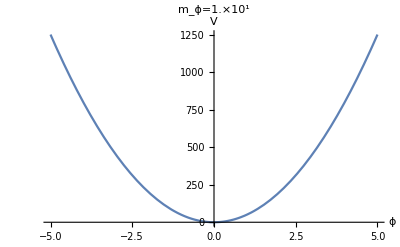

```mathematica
(* potencjał *)
Block[{tytul=""},
VT[x1_]:=V[x1] /.fun /. param;
tytul=mrkWykresy`tytulWykresu[param];
Plot[Evaluate[VT[xx]],{xx,-5,5},AxesLabel->{"ϕ","V"},PlotRange->All,Axes->{True,False},PlotLabel->tytul]]
```

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
(* tensor metryczny w longitudinal gauge *)
Block[{Lag,potencjal,Masa,ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* gęstość lagranżjanu *)
Lag=Expand[ℒ==Lagrangian[g,x,pola,fG,La,0]];
(* potencjał *)
potencjal=V[Sequence@@pola]==(V[Sequence@@pola] /. fun) ;
(* macierz masy *)
Masa=MacierzMasy[g,x,pola,fG,La,False];
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=RuchuRownaniakw[g,x,pola,fG,La,1];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=If[mMS,MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1],False];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La,False];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,mMS,1,True],600,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,mMS,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Macierz masy",Masa},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"F",sciezka];
wpisB={"Macierz masy",Masa};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"M",sciezka];
)]//AbsoluteTiming
```

22:39:00GMT+1.TimeObject[{22,39,0.0131498},TimeZone→1.] Równania ruchu w rzędzie 0

22:39:00GMT+1.TimeObject[{22,39,0.716734},TimeZone→1.] Równanie pola 00 w rzędzie 0

22:39:00GMT+1.TimeObject[{22,39,0.870843},TimeZone→1.] Równania ruchu w rzędzie 1

22:39:00GMT+1.TimeObject[{22,39,0.953927},TimeZone→1.] Równanie pola 00 w rzędzie 1

22:39:01GMT+1.TimeObject[{22,39,1.08151},TimeZone→1.] Równanie pola 01 w rzędzie 1

22:39:01GMT+1.TimeObject[{22,39,1.12404},TimeZone→1.] Równanie pola 11 w rzędzie 0

22:39:01GMT+1.TimeObject[{22,39,1.19159},TimeZone→1.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

22:39:01GMT+1.TimeObject[{22,39,1.35723},TimeZone→1.] Baza Freneta

22:39:01GMT+1.TimeObject[{22,39,1.36422},TimeZone→1.] Baza Freneta

22:39:01GMT+1.TimeObject[{22,39,1.38323},TimeZone→1.] Pochodne potencjału w zmiennych σ i s

Solve::svars: Equations may not give solutions for all "solve" variables.

22:39:01GMT+1.TimeObject[{22,39,1.42326},TimeZone→1.] Równania ruchu dla składowych krzywizny i izokrzywizny

22:39:01GMT+1.TimeObject[{22,39,1.99824},TimeZone→1.] Równania ruchu dla zmiennych współporuszających się

{2.44944,Null}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tfTot}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* liczba e-powiększeń, N(0) ustawione jest na -8 - NALEŻY USTAWIĆ! *)
Nall=68.;
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
wstepneWP={16.42}; (* -5 *)
(*wstepneWP={16.42}; (* -7 *)*)
(*wstepneWP={250}; (* -10 *)*)
(*wstepneWP={{250},{-10.^-10}};*)
wstepneWSP={0.01};
(*wstepneWSP={{0.01},{0}};*)
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

00:37:31GMT+1.TimeObject[{0,37,31.9239},TimeZone→1.]

{ϕ[0.]==16.42,ϕ'[0.]==-8.16497,nn[0.]==0.}

67.9735

{{{978708267211914112/59604644775390625},{-486669886665180928/59604644775390625}},810306927700849152/11920928955078125,114086802779052352/59604644775390625}

```mathematica
%//N
```

1.91406

```mathematica
(* końcowy czas *)
tf=tfTot;
```

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
N0t=-8;
N0p=N0t;
```

### Tło

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(
testN={-1,-0.1,0,0.1,0.3,2};
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{676150.08,766147.92,776147.88,786147.84,806147.88,976153.32}

```mathematica
(* zakresy i czasy wykorzystywane przy rysowaniu wykresów - NALEŻY USTAWIĆ! *)
{m1,m01,pm0,p01,p03}={676150.08,766147.9199999999,776147.88,786147.84,806147.88};(*psi 0*)
{m1,m01,pm0,p01,p03,p2}={676150.08,766147.9199999999,776147.88,786147.84,806147.88,976153.20};(*psi 0.0001 M=20*)
(*{m1,m01,pm0,p01,p03}={676150.08,766147.9199999999,776147.88,786147.84,806147.88};(*psi 0.01*)
{m1,m01,pm0,p01,p03}={676150.01999999999999999999999999999999572025`24.,766147.9799999999999999999999999999999951506`24.,776147.83999999999999999999999999999999508731`24.,786147.82999999999999999999999999999999502401`24.,806147.93999999999999999999999999999999489742`24.};(*psi 1*)
{m1,m01,pm0,p01,p03}={676150.0800000000000000000000000000000046364`24.,766147.92000000000000000000000000000000525351`24.,776147.88000000000000000000000000000000532209`24.,786147.84000000000000000000000000000000539066`24.,806147.8800000000000000000000000000000055278`24.};(*psi 0.1 M150*)*)
(*{m1,m01,pm0,p01,p03,p2}={676150.08,766147.92,776147.88,786147.84,806147.88,976153.32};(*psi 0.0001 M=200*)*)
tzakresBazaM={{m01},{p01}};
tzakresBazaF={m01,p01};
tzakresB={m01,p01};
tB=p03;
(*tN0=pm0;

lista500zc=Join[Range[m01,m002,100],Range[m002,p002,16],Range[p002,p015,77],{tf}];(*{81,250,169}*)
gridzc={{},{m002,pm0,p002,p015},{m01,p015},{m01,p015},{m01,p015}};

lista500={{tf},lista500zc};*)
```

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
Block[{zakres={},lista=lista500},
(*lista=Join[listazc,{lista1000[[2]]}];*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p01},Table[p01,Length[lista]-1]]};
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres];]//AbsoluteTiming
```

{652.589,Null}

```mathematica
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->{{0},{tf}}];//AbsoluteTiming
```

00:37:59GMT+1.TimeObject[{0,37,59.9944},TimeZone→1.] Czasy

00:38:01GMT+1.TimeObject[{0,38,1.37882},TimeZone→1.] Epilog

00:38:01GMT+1.TimeObject[{0,38,1.39443},TimeZone→1.] Wykres

{1.76049,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

17:50:16GMT+1.TimeObject[{17,50,16.9023},TimeZone→1.] Liczba e-powiększeń

17:50:16GMT+1.TimeObject[{17,50,16.9023},TimeZone→1.] Wykres 1

17:50:17GMT+1.TimeObject[{17,50,17.121},TimeZone→1.] Wykres energii kinetycznej

{0.419861,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,zakrest->tzakresBazaF];//AbsoluteTiming
```

17:56:34GMT+2.TimeObject[{17,56,34.798},TimeZone→2.] Baza Freneta

17:56:39GMT+2.TimeObject[{17,56,39.1092},TimeZone→2.] Prędkości kątowe bazy

17:56:39GMT+2.TimeObject[{17,56,39.1591},TimeZone→2.] Liczba e-powiększeń i zmienne

17:56:39GMT+2.TimeObject[{17,56,39.1591},TimeZone→2.] Wykres

{68.5314,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->tzakresBazaM, gridt->{}];//AbsoluteTiming
```

17:55:35GMT+2.TimeObject[{17,55,35.0438},TimeZone→2.] Wykres prędkości kątowych bazy

{21.7207,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń
z uwzględnieniem produkcji cząstek *)
Block[{grid={{},{}},zakres,lista=lista500},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p01},Table[p01,Length[lista]-1]]};
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres,gridt->grid];]//AbsoluteTiming
```

{679.435,Null}

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Block[{opisy={}},
(*opisy={Superscript["m","2"],Superscript["M","2"]};*)
Masy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t, legenda->opisy];]//AbsoluteTiming
```

17:59:31GMT+2.TimeObject[{17,59,31.0593},TimeZone→2.] Liczba e-powiększeń i masy

17:59:31GMT+2.TimeObject[{17,59,31.0593},TimeZone→2.] Wykres

{8.628,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

20:04:15GMT+2.TimeObject[{20,4,15.6358},TimeZone→2.] Macierz masy w bazie Freneta

20:04:15GMT+2.TimeObject[{20,4,15.6358},TimeZone→2.] Prędkości kątowe bazy

20:04:15GMT+2.TimeObject[{20,4,15.6671},TimeZone→2.] Efektywna macierz masy

20:04:15GMT+2.TimeObject[{20,4,15.968},TimeZone→2.] Liczba e-powiększeń i masy

20:04:15GMT+2.TimeObject[{20,4,15.969},TimeZone→2.] Wykres

$Aborted

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=0;
bm=SetPrecision[BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
Print["BM: ",bm];
bf=SetPrecision[BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
 Print["BF: ",bf];)]
```

Test

BM: {{-0.98769,0.15643,2.7141×10^-8},{-0.15637,-0.98729,-0.028477},{-0.0044547,-0.028126,0.99959}}

BF: {{0.9879,-0.15505,-0.0022354},{-0.15505,-0.9875,-0.028472},{0.0022071,0.028474,-0.99959}}

k_turn: 0.00001 ; k(N=3.)=0.000201: {0.000294,0.00287,0.0162}

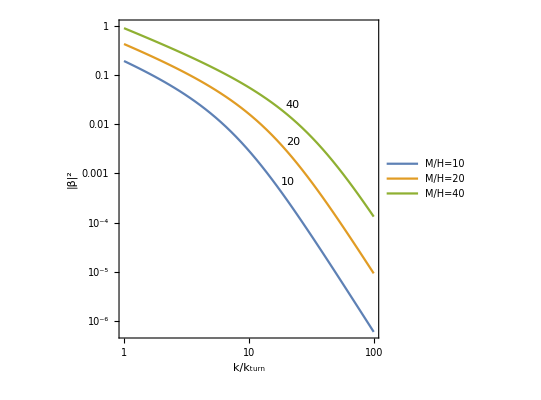

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-7),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)};

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* gęstość energii wyprodukowanych ciężkich cząstek w uproszczonej wersji *)
Block[{mh},(mh={10^(-4), 2*10^(-4), 4*10^(-4), 5*10^(-4), 10^(-3),1.5*10^(-3),1.65*10^(-3),1.7*10^(-3),1.8*10^(-3),1.9*10^(-3), 2*10^(-3)};
Print["l ", N[mh^4*Sin[Δθ]^2/(24*Pi^2) /. param]];
Print["h ", N[mh^4*Sin[Δθ]^2/(16*Pi^2) /. param]];)]
```

l {4.03138×10^-20,6.45021×10^-19,1.03203×10^-17,2.51961×10^-17,4.03138×10^-16,2.04089×10^-15,2.98806×10^-15,3.36705×10^-15,4.23198×10^-15,5.25373×10^-15,6.45021×10^-15}

h {6.04707×10^-20,9.67531×10^-19,1.54805×10^-17,3.77942×10^-17,6.04707×10^-16,3.06133×10^-15,4.48209×10^-15,5.05057×10^-15,6.34797×10^-15,7.8806×10^-15,9.67531×10^-15}

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

18:00:20GMT+2.TimeObject[{18,0,20.6511},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

18:00:20GMT+2.TimeObject[{18,0,20.6668},TimeZone→2.] Wykres wierszy 1

18:00:30GMT+2.TimeObject[{18,0,30.7578},TimeZone→2.] Wykres wierszy 2

18:00:31GMT+2.TimeObject[{18,0,31.1237},TimeZone→2.] Wykres wierszy 3

18:00:31GMT+2.TimeObject[{18,0,31.4277},TimeZone→2.] Wykres kolumn 1

18:00:31GMT+2.TimeObject[{18,0,31.69},TimeZone→2.] Wykres kolumn 2

18:00:31GMT+2.TimeObject[{18,0,31.9595},TimeZone→2.] Wykres kolumn 3

{11.6114,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

18:01:18GMT+2.TimeObject[{18,1,18.048},TimeZone→2.] Liczba e-powiększeń i baza

18:01:18GMT+2.TimeObject[{18,1,18.0637},TimeZone→2.] Wykres wierszy 1

18:01:49GMT+2.TimeObject[{18,1,49.2032},TimeZone→2.] Wykres wierszy 2

18:01:50GMT+2.TimeObject[{18,1,50.6504},TimeZone→2.] Wykres wierszy 3

18:01:50GMT+2.TimeObject[{18,1,50.9866},TimeZone→2.] Wykres kolumn 1

18:01:51GMT+2.TimeObject[{18,1,51.3047},TimeZone→2.] Wykres kolumn 2

18:01:51GMT+2.TimeObject[{18,1,51.6368},TimeZone→2.] Wykres kolumn 3

{33.946,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,
Lao,p3},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

(*(* lista współczynników oddziaływania w formie {{C_σs1, C_σs2, ...}, {C_s1σ, C_s1s2, ...}, ...} *)
funkcje={Flatten[Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,mMS,1][[-1]]]]};
(*opisy={{"C1","coefficients",{"C_σs1","C_σs2"}},{"C2","coefficients",{"C_s1σ","C_s1s2"}},{"C3","coefficients",{"C_s2σ","C_s2s1"}}};*)
(*opisy={{"C","coefficients",{"C_σs1","C_σs2","C_s1σ","C_s1s2","C_s2σ","C_s2s1"}}};*)
opisy={{"C1","coefficients",{"C_s2s1"}}};*)

funkcje={{Symbol["nn"]'[x[[1]]]}};
opisy={{"H","",{"H"}}};

(*funkcje={{-Symbol["nn"]''[x[[1]]]/Symbol["nn"]'[x[[1]]]^2}};
opisy={{"eps","",{"ϵ"}}};*)

(*Lao=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{4}][[1]]/. Symbol["P"]->0;*)

(*funkcje={{Abs[Symbol["τ"][x[[1]]]]}};
opisy={{"tau","",{"tau"}}};*)

WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

00:38:25GMT+1.TimeObject[{0,38,25.5176},TimeZone→1.] Liczba e-powiększeń

00:38:25GMT+1.TimeObject[{0,38,25.5176},TimeZone→1.] Wykres 1

{0.392938,Null}

### Perturbacje

```mathematica
(* widma *)
(* widma w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"t",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

```mathematica
(* perturbacje w zależności od liczby e-powiększeń *)
PerturbacjeB[pola,fG,La,g,x,fR,tloi,lista500zc,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"wsp",5.5},NkwNorm->0.,norm->"",tftot->tfTot,baza->"",RS->False,pertu->False];//AbsoluteTiming
```

04:42:48GMT+2.TimeObject[{4,42,48.5409},TimeZone→2.] Liczba e-powiększeń i widma

kw 0.0000549728

tf A {28.4502,4.50617}

tf {Re,Im} {{{27.4032,7.02014},{4.34746,1.08329}},{{2.9669,0.628479},{0.473532,0.085902}}}

04:42:48GMT+2.TimeObject[{4,42,48.7655},TimeZone→2.] Wykres perturbacji

04:42:59GMT+2.TimeObject[{4,42,59.0633},TimeZone→2.] Wykres wierszy 1

04:43:01GMT+2.TimeObject[{4,43,1.73833},TimeZone→2.] Wykres wierszy 2

04:43:03GMT+2.TimeObject[{4,43,3.93532},TimeZone→2.] Wykres kolumn 1

04:43:05GMT+2.TimeObject[{4,43,5.93501},TimeZone→2.] Wykres kolumn 2

04:43:08GMT+2.TimeObject[{4,43,8.13598},TimeZone→2.] Wykres Re

04:43:14GMT+2.TimeObject[{4,43,14.92},TimeZone→2.] Wykres Im

{452.07,Null}

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Block[{grid={},opisy={},zakres={},lista={{tf}},listaNkw},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
opisy={"0.1","0.5","1"};
opisy={"1","2","10","20"};
opisy={"1"};
listaNkw=Map[{"wsp",#} &, {0.1,0.5,1.}];
listaNkw=Map[{"wsp",#} &, {1.,2.,10.,20.}];
listaNkw=Map[{"wsp",#} &, {1.}];
lista=Table[{tf},Length[listaNkw]];
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
zakres={Table[0,Length[lista]],Join[{tf},Table[tf,Length[lista]-1]]};
WidmaB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->listaNkw,NkwNorm->0.,norm->"t",tftot->tfTot,baza->"F",RS->True,pertu->False,zakrest->zakres,gridt->grid,legenda->opisy];]//AbsoluteTiming
```

Power::infy: Infinite expression 1/0.^2 encountered.

tf {{0.}}

02:11:39GMT+1.TimeObject[{2,11,39.3109},TimeZone→1.] Wykres widm 1

Power::infy: Infinite expression 1/0.^2 encountered.

$Aborted[]

General::stop: Further output of Power::infy will be suppressed during this calculation.

02:11:42GMT+1.TimeObject[{2,11,42.9828},TimeZone→1.] Wykres widm

02:11:43GMT+1.TimeObject[{2,11,43.5556},TimeZone→1.] Wykres wierszy 1

02:11:44GMT+1.TimeObject[{2,11,44.1337},TimeZone→1.] Wykres kolumn 1

{9.15616,Null}

```mathematica
(* widma w bazie Freneta w zależności od liczby falowej *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

22:29:47GMT+1.TimeObject[{22,29,47.7408},TimeZone→1.]

22:29:47GMT+1.TimeObject[{22,29,47.7408},TimeZone→1.] Widma

kNorm 6.29989904017119227749×10^-722:29:47GMT+1.TimeObject[{22,29,47.7564},TimeZone→1.]

1: {6.06032×10^-13}22:29:51GMT+1.TimeObject[{22,29,51.2515},TimeZone→1.]

2: {5.92011×10^-13}22:29:58GMT+1.TimeObject[{22,29,58.17},TimeZone→1.]

0.1: {6.5378×10^-13}22:29:58GMT+1.TimeObject[{22,29,58.6113},TimeZone→1.]

$Aborted

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby falowej *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{{"",0.}},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"",RS->True,pertu->False,zakrest->{{0.},{tf}}];//AbsoluteTiming
```

22:31:12GMT+1.TimeObject[{22,31,12.6999},TimeZone→1.]

norm P* 1

InterpolatingFunction

{1}

{Thickness[Large]}

kNorm 6.29989904017119227749×10^-722:31:12GMT+1.TimeObject[{22,31,12.6999},TimeZone→1.]

0.1: {{6.5378×10^-13}}22:31:12GMT+1.TimeObject[{22,31,12.6999},TimeZone→1.]

1: {{6.06032×10^-13}}22:31:12GMT+1.TimeObject[{22,31,12.6999},TimeZone→1.]

2: {{5.92011×10^-13}}22:31:12GMT+1.TimeObject[{22,31,12.7155},TimeZone→1.]

$Aborted

```mathematica
(* wzmocnienia widma perturbacji krzywizny w zależności od liczby falowej *)
Print[TimeObject[Now]];
Block[{punkty,opisy={},lista={{tf}},norm},
(*punkty=Map[{"wsp", #} &, Join[Range[0.1,3.,0.1],Range[3.,20.,0.1]]];*)
punkty=Map[{"wsp", #} &, Range[0.1,10.,1.]];
punkty=Map[{"N", #} &, {-2.3,-1.2,-0.5,-0.2,0.,0.7,1.1,1.6,2.3}];
(*punkty=Map[{"wsp", #} &, {0.1, 0.5, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
norm=Table[Table[0.,Length[punkty]],Length[lista]];
norm={{-2.3,-1.2,-0.5,-0.2,0.,0.7,1.1,1.6,2.3}};
WzmocnienieB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty, NkwNorm->norm,baza->"M",nrwidm->{1},legenda->opisy]]//AbsoluteTiming
```

00:22:43GMT+1.TimeObject[{0,22,43.4367},TimeZone→1.]

00:22:43GMT+1.TimeObject[{0,22,43.4367},TimeZone→1.]Rozwiązanie 1

ll

00:24:52GMT+1.TimeObject[{0,24,52.394},TimeZone→1.] Wykres widm(k) - wzmocnienia(k)

{129.258,Null}

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->{"N",3.}];//AbsoluteTiming
```

02:15:31GMT+2.TimeObject[{2,15,31.8027},TimeZone→2.]

02:15:31GMT+2.TimeObject[{2,15,31.8087},TimeZone→2.] Korelacje

02:15:31GMT+2.TimeObject[{2,15,31.8097},TimeZone→2.] Korelacje względne

02:15:31GMT+2.TimeObject[{2,15,31.8167},TimeZone→2.] Liczba e-powiększeń i względne korelacje

02:15:31GMT+2.TimeObject[{2,15,31.8167},TimeZone→2.] Wykres

NDSolve::vdobj: Encountered Qσkw[0.]==117382., which is not a valid NDSolve`StateData expression.

General::stop: Further output of NDSolve::vdobj will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {NDSolve`ProcessSolutions[Qσkw[0.]==117382.],NDSolve`ProcessSolutions[Qσkw[0.]==117382.],NDSolve`ProcessSolutions[Qσkw[0.]==117382.]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{0.512465,Null}

```mathematica
Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"h",tftot->tfTot];//AbsoluteTiming
```

01:40:34GMT+2.TimeObject[{1,40,34.8096},TimeZone→2.]

01:40:34GMT+2.TimeObject[{1,40,34.8252},TimeZone→2.] Korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8428},TimeZone→2.] Liczba e-powiększeń i korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8443},TimeZone→2.] Wykres

{1.56311,Null}

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2, k2/k1} *)
Block[{Nkw},(Nkw=1.;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{9.9950724445654623272×10^-6,0.000027168539295141792043,-0.000017173466850576329716,2.7181933343478581909}

```mathematica
(* liczby obsadzeń *)
(* liczba obsadzeń w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->0.,zakrest->tzakresB];//AbsoluteTiming
```

05:06:21GMT+2.TimeObject[{5,6,21.3583},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.10504},TimeZone→2.] Liczba e-powiększeń i liczba obsadzeń

{3.50943×10^-9,1.49779×10^-6}05:14:04GMT+2.TimeObject[{5,14,4.13455},TimeZone→2.]

{1.33444×10^-10,1.99601×10^-10}05:14:04GMT+2.TimeObject[{5,14,4.16809},TimeZone→2.]

{0.00644601,0.00657539}05:14:04GMT+2.TimeObject[{5,14,4.19861},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.19911},TimeZone→2.] Wykres

{475.446,Null}

```mathematica
(* liczba obsadzeń w zależności od liczby falowej *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,zakrest->{tB}];//AbsoluteTiming
```

03:26:01GMT+2.TimeObject[{3,26,1.53742},TimeZone→2.]

03:26:01GMT+2.TimeObject[{3,26,1.67498},TimeZone→2.] Liczba obsadzeń

kwNorm: {0.463267,0.829206}03:26:03GMT+2.TimeObject[{3,26,3.71264},TimeZone→2.]

1.5: {1.02366,0.375015}03:26:05GMT+2.TimeObject[{3,26,5.92366},TimeZone→2.]

2: {0.365702,0.228618}03:26:08GMT+2.TimeObject[{3,26,8.31438},TimeZone→2.]

10: {0.0139638,0.0138118}03:26:14GMT+2.TimeObject[{3,26,14.0065},TimeZone→2.]

20: {0.00205275,0.00223467}03:26:23GMT+2.TimeObject[{3,26,23.8839},TimeZone→2.]

03:26:23GMT+2.TimeObject[{3,26,23.8844},TimeZone→2.] Wykres

$Aborted

```mathematica
Test
(* gęstość energii wyprodukowanych na zakręcie cząstek w chwili t0 *)
Print[TimeObject[Now]];
GestoscEnergiiCzastekTest[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS, t0->tN0]//AbsoluteTiming
```

Test

04:56:04GMT+2.TimeObject[{4,56,4.98974},TimeZone→2.]

04:56:13GMT+2.TimeObject[{4,56,13.7468},TimeZone→2.] Gęstości energii wyprodukowanych cząstek

{{0.000099552,0},{0,0.00098715}}

{9.9951×10^-6,{0.00010005,0.0009872}}

4.45893×10^-14

8.78729×10^-14

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"F"]//AbsoluteTiming
```

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny *)
Print[TimeObject[Now]];
Block[{punkty,punkty2,lista={{tf}}},
punkty=Map[{"wsp", #} &, Join[Range[0.1,3.,0.1],Range[3.,10.,0.1]]];
(*punkty=Map[{"wsp", #} &, {0.1, 0.5, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
punkty2=Table[10^(-6),Length[punkty]];
IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty,Nkw2->punkty2, NkwNorm->Table[0.,Length[lista]],baza->"M",nrwidm->{1,3}]]//AbsoluteTiming
```

19:54:47GMT+2.TimeObject[{19,54,47.9424},TimeZone→2.]

19:54:47GMT+2.TimeObject[{19,54,47.958},TimeZone→2.]Rozwiązanie 1

19:54:49GMT+2.TimeObject[{19,54,49.7737},TimeZone→2.] Wykres ns(k)

{2.16656,Null}

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",Nk},baza->"F"];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.}, NkwNorm->0.];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
(*wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];*)
wartosci=Flatten[{Map[ScientificForm[If[Element[#[[2]],Rationals],N[#[[2]]],#[[2]]], 2, NumberMultiplier->"*",NumberPoint->","] &, param], {NumberForm[N0t,NumberPoint->","],NumberForm[N0p,NumberPoint->","]},Map[ScientificForm[If[Element[#,Rationals],N[#],#], 3, NumberMultiplier->"*",NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=nazwaplikurow<>"_dane.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

{0.0324733,Null}

```mathematica
Quit[]
```